```mathematica
SetDirectory[NotebookDirectory[]];
options3={Frame->{True,True,False,False},FrameStyle->Black,BaseStyle->{FontSize->20},LabelStyle->Black};
fNumericMean[aX_,α_,β_,y0_]:=Module[{y,x,f=NDSolveValue[{y'[x]==α y[x](1-β y[x]),y[0]==y0},y,{x,0,100}]},f[aX]]
fMean[x_,α_,β_,y0_]:=(ⅇ^(x α) y0)/(1-y0 β+ⅇ^(x α) y0 β)
fYGenerate[x_,α_,β_,y0_,σ_]:=RandomVariate[NormalDistribution[fMean[x,α,β,y0],σ],{1}][[1]]
fGenerateY[]:=Block[{lX =Table[x,{x,{1,1+2.7,1+2 2.7, 9.5}}],lY},lX=lX+RandomVariate[NormalDistribution[0,0.1],Length@lX];Thread[{lX,fYGenerate[#,0.5,0.05,5,3]&/@lX}]]
fGenerateY1[sigma__]:=Block[{lX =Table[x,{x,{1,1+2.7,1+2 2.7, 9.5}}],lY},lX=lX+RandomVariate[NormalDistribution[0,0.1],Length@lX];Table[{lX[[i]],fYGenerate[lX[[i]],0.5,0.05,5,sigma[[i]]]},{i,1,Length@lX,1}]]
Needs["PolygonPlotMarkers`"]

allShapes=PolygonMarker[All];
Tooltip[Graphics[{FaceForm[Hue@Random[]],EdgeForm[{Black,Thickness[0.003],JoinForm["Miter"]}],PolygonMarker[#,1]},ImageSize->30,PlotRange->1.5,PlotRangePadding->0,ImagePadding->0],#]&/@allShapes;
allShapes = RandomSample[allShapes[[1;;30]]];
graphs=Graphics[{FaceForm[Blue],PolygonMarker[ToString@#,Scaled[0.04]]},AlignmentPoint->{0,0}]&/@allShapes[[3;;13]];
```

```mathematica
data=Table[fGenerateY1[{1,2,3,1.5}],{i,1,50,1}];
```

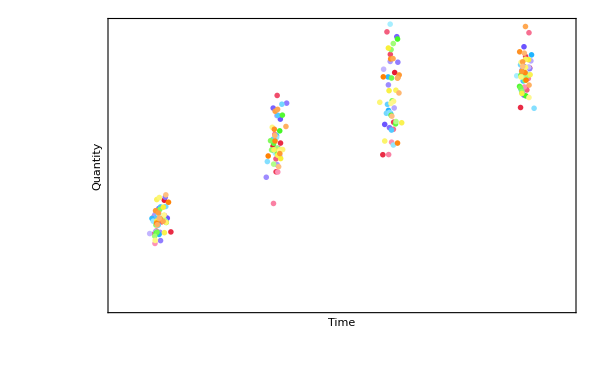

```mathematica
gsingle=ListPlot[data,PlotStyle->"BrightBands",PlotRange->{{0,10.5},Full},PlotMarkers ->Graphics[{FaceForm[Blue],PolygonMarker[ToString@"Disk",Scaled[0.04]]},AlignmentPoint->{0,0}],ImageSize->600,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"Time","Quantity"},ImagePadding->{{30,None},{30,None}}]
```

```mathematica
aPlot1=Plot[PDF[NormalDistribution[0,0.002],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
aPlot2=Plot[PDF[NormalDistribution[0,0.003],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
aPlot3=Plot[PDF[NormalDistribution[0,0.005],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
aPlot4=Plot[PDF[NormalDistribution[0,0.0025],x],{x,-0.015,0.015},Axes->None,PlotStyle->Directive[Black,Dashed],Filling->Bottom,FillingStyle->Opacity[0.7,Gray],AspectRatio->1/3,PlotRange->{Automatic,{0,221}}];
```

```mathematica
Show[gsingle,Graphics[Inset[Rotate[aPlot1,3Pi /2],{1.7,fMean[1,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot2,3Pi /2],{4.5,fMean[1+2.7,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3Pi /2],{4.5+2.7,fMean[1+2.7 2,0.5,0.05,5]}]],Graphics[Inset[Rotate[aPlot3,3Pi /2],{10.2,fMean[9.5,0.5,0.05,5]}]]]
```

-Graphics-

## Estimate contour volume

### Try Rosenbrock

```mathematica
f[x_,y_]:=-((1-x)^2 + 100(y-x^2)^2)
```

```mathematica
lcountours=Table[-2440+200i,{i,1,12,1}];
lcountours=Append[lcountours,0];
colours=ColorData["DarkRainbow"]/@Range[0,1,1/(Length@lcountours)];
lcountours
```

{-2240,-2040,-1840,-1640,-1440,-1240,-1040,-840,-640,-440,-240,-40,0}

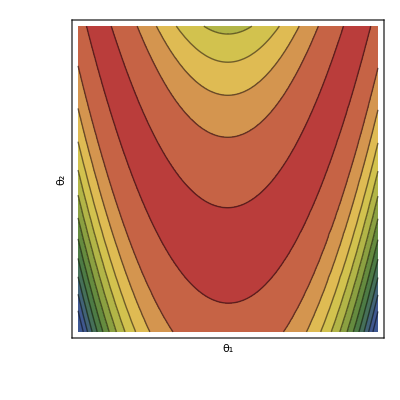

```mathematica
g1=ContourPlot[f[x,y],{x,-2,2},{y,-1,3},Contours->lcountours,PlotRange->Full,ImageSize->400,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"θ_1","θ_2"},ImagePadding->{{30,None},{30,None}},ContourShading->colours]
```

```mathematica
params=RandomVariate[UniformDistribution[{{-2,2},{-1,3}}],1000];
```

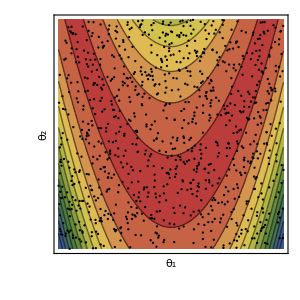

```mathematica
g1a=Show[g1,ListPlot[params,PlotStyle->Black],ImageSize->300]
```

```mathematica
fSampleF[]:=Block[{x=RandomVariate[UniformDistribution[{-2,2}],{1}][[1]],y=RandomVariate[UniformDistribution[{-1,3}],{1}][[1]]},f[x,y]]
```

```mathematica
samples=Table[fSampleF[],{100000}];
dist=SmoothKernelDistribution[samples,10];
```

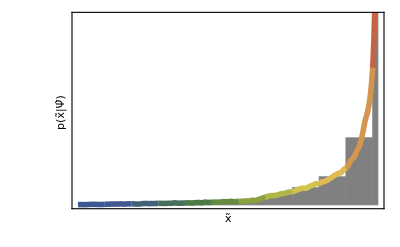

```mathematica
g2=Show[Histogram[samples,{lcountours},"PDF",PlotRange->{{-2240,0.2},{0,0.005}},ChartStyle->Gray],Table[Plot[PDF[dist,x],{x,lcountours[[i]],lcountours[[i+1]]},PlotRange->{{-2300,0},{0,0.0055}},PlotStyle->Directive[Thickness[0.01],colours[[i]]]],{i,1,(Length@lcountours)-1,1}],ImageSize->400,FrameTicks->None,FrameStyle->Directive[Black,20,Thick],Frame->{True,True,False,False},FrameLabel->{"x̃","p(x̃|Ψ̂)"},ImagePadding->{{30,None},{30,None}}]
```

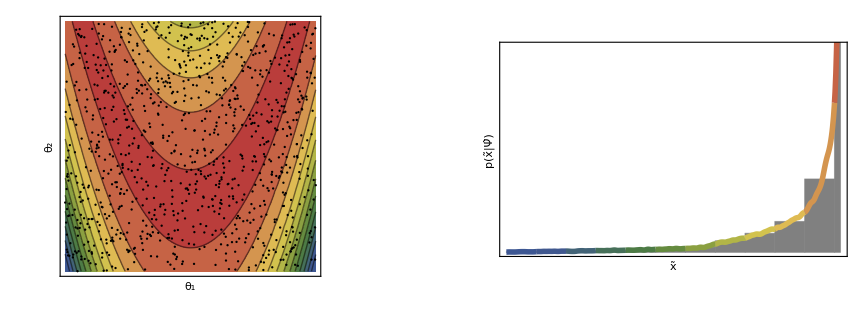

```mathematica
GraphicsRow[{g1a,g2}]
```

## MCMC on parameter space

```mathematica
mcmc=Accumulate@RandomVariate[MultinormalDistribution[{0,0},0.05 IdentityMatrix[2]],80];
```

```mathematica
mcmc={{0.3916734366881812,0.04056880515692671},{0.35800782395622893,0.1504556081776109},{0.2916564260632538,0.40798821842861116},{0.32402004330936246,0.36859528633996214},{-0.08095620201950587,0.3536494409202866},{0.06980378752620076,0.06634863325958845},{-0.25672312833304967,-0.014062798869079407},{-0.34838133297540574,0.09183865449798816},{-0.07669656617720316,0.2134494231294816},{-0.09290594241276068,0.29048067780617415},{-0.40643074921025313,0.08379999360294274},{-0.18130137627328968,0.16590187588126531},{-0.2639037542351235,-0.05899827627602211},{-0.2681376103629823,-0.1277923319285615},{-0.31581033317256896,-0.262937402435566},{-0.10579623544940425,-0.15235916780088452},{-0.26482711920920077,0.020250760227070008},{-0.5906460736005187,0.10467342451029894},{-0.5601626129128758,0.5555926525557212},{-0.5412639258896371,0.4996057261208453},{-0.4387679945837675,0.3339135313399254},{-0.420108642367288,0.13465747088654428},{-0.4872427436882988,0.31064231486265415},{-0.053064465512030756,0.63891911008108},{0.42718835085882817,0.695600634502062},{0.63289089467679,0.4086722515356289},{0.2652738108767216,0.5092151814896917},{0.000661818707877404,0.549786520003003},{-0.47419067405379367,0.9037589934433745},{-0.5509806742278134,0.9376168172647377},{0.16239314377608127,0.8601794581285991},{0.08611920643224534,0.8585949695553093},{0.12011434752344978,1.295418447620336},{0.05055922074997521,1.4292490990711426},{-0.34092494731215506,1.3473848145402634},{-0.5668419970324474,1.176609073903411},{-0.27690274133634396,1.0133067860524514},{-0.4357715938433402,1.205875893122095},{-0.28565707131039153,1.0571418085371849},{-0.2418176981105395,0.6326553266887448},{-0.11051133499770424,0.8834881286932412},{0.0011975322928803739,0.8532396614854273},{-0.024033864198626208,0.6328092059450223},{-0.1775961658315291,0.49092931802979484},{-0.5521578346047719,-0.34134017534388045},{-0.5481206674071708,-0.6619186381445656},{-0.42666812689329153,-0.9854856389912889},{-0.423793775167098,-1.0417522294504142},{-0.6671880478489807,-1.0002882452964026},{-0.8124560948380306,-0.9586677395472356},{-1.1300645703379586,-1.1419773932410975},{-1.3644231941210316,-1.0599429755498522},{-1.0559720467758928,-0.9551314089400349},{-1.0254532397326592,-0.9485719693915499},{-0.704333740038515,-0.9040223249740459},{-0.7454391737756362,-0.9934016749430968},{-0.4923855145287129,-1.0103859206929418},{-0.5393009723285365,-0.7526181630516776},{-0.9006125426188544,-0.9384669772163732},{-0.7195046603668339,-1.3156776683900793},{-0.5418907483249329,-1.3886232257235795},{-0.07471012192708976,-1.2673801419212993},{-0.20032770104298736,-1.368477111075351},{-0.4042442439843694,-1.560114504124023},{-0.500699554770644,-1.2721344065371252},{-0.8500166961351103,-1.3269802220421687},{-1.01196911337447,-1.3219396794738745},{-0.9070327468788124,-1.4159681389419616},{-1.0403277601474652,-1.7263202258909618},{-1.106248467373215,-1.664153734272309},{-0.9220270709321943,-1.5459999454833167},{-0.9543200508629287,-1.746959506822516},{-0.6850573941973747,-1.6378578159250388},{-0.7687196261450777,-1.6447239648946237},{-0.9168705425474202,-1.8829668603454437},{-1.0446779993089668,-1.7101218123760753},{-0.9538675015800016,-1.6558147965355214},{-0.97267290734444,-1.5345504381893673},{-0.86444436905766,-1.5399364601256196},{-0.7680185063979779,-1.7500996348465123}};
```

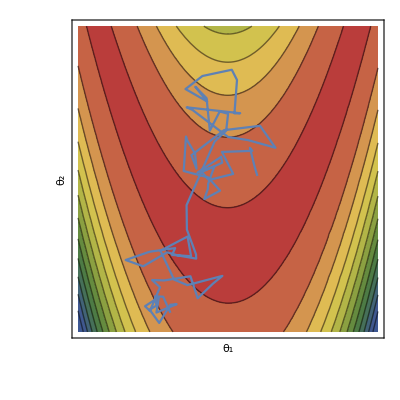

```mathematica
Show[g1,ListLinePlot[#+{0,1}&/@mcmc,PlotRange->{{-2,2},{-1,3}}]]
```

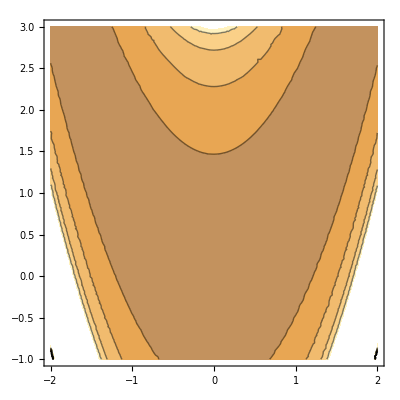

```mathematica
ContourPlot[(2400+f[x,y])/PDF[dist,f[x,y]],{x,-2,2},{y,-1,3}]
```

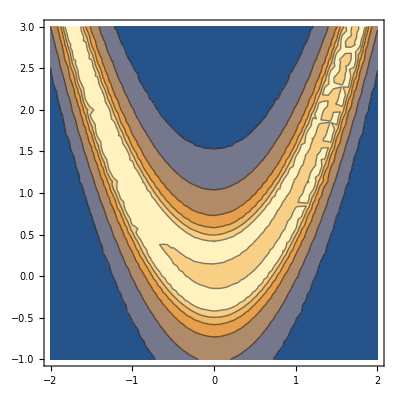

```mathematica
ContourPlot[PDF[dist,f[x,y]],{x,-2,2},{y,-1,3}]
```

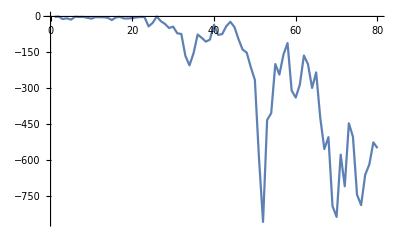

```mathematica
ListLinePlot[(f[#[[1]],#[[2]]]&/@mcmc)]
```

## Try another optimisation problem

```mathematica
f1[x_,y_]:=PDF[MultinormalDistribution[{0,0},{{1,0.85},{0.85,1}}],{x,y}]+PDF[MultinormalDistribution[{0,0},{{1,-0.85},{-0.85,1}}],{x,y}]
```

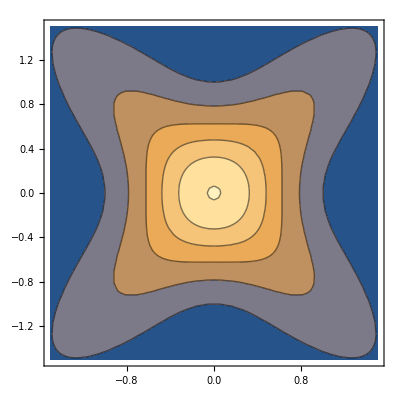

```mathematica
ContourPlot[f1[x,y],{x,-1.5,1.5},{y,-1.5,1.5},PlotRange->Full]
```

```mathematica
fSampleF1[f_,xrange__,yrange__]:=Block[{x=RandomVariate[UniformDistribution[xrange],{1}][[1]],y=RandomVariate[UniformDistribution[yrange],{1}][[1]]},f[x,y]]
```

```mathematica
samples=Table[fSampleF1[f1,{-1.5,1.5},{-1.5,1.5}],{1000}];
dist=SmoothKernelDistribution[samples];
```

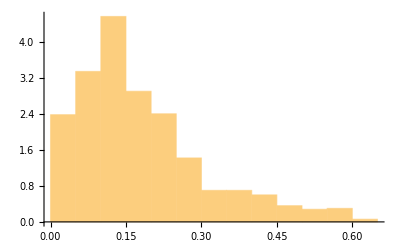

```mathematica
Histogram[samples,Automatic,"PDF"]
```